# Three Stage Control

Gabriel J. Severino

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## General Definition for the System:

3 stage system; 20 topologies that demonstrate tissue homeostasis

-Graphics-


Where LS is the division rate of Stem cells,
 PS is the probability that Stem cells will differentiate into intermediate cells,
 LI is the division rate of Intermediate cells, 
 PI is the probability that an intermediate cell will differentiate into a TD
 and D is the death rate of differentiated cells
 
Additionally: k1, k2, and k3 are the parameters for control. 


Generalized Differential Equations: 

dSTEM/dt = LS*STEM*(1-STEM/k1) - PS*2*LS*STEM*(1-INTER/k2)  

dINTER/dt = PS*2*LS*STEM*(1-INTER/k2) + LI*STEM*(1-DIFF/k3) - PI*2*LI*STEM*1  

dDIFF/dt = PI*2*LI*STEM*1 - Death*DIFF 



We are going to be examining the effects of three different control functions: 

Komorova :1-({pop}/{k})

Lander: 1/(1+{a}*{pop})

Hill: 1/(1+({a}*{pop})^{n})

## Topology 1

-Graphics-

```mathematica
DS1=DynamicalSystem[{LS*STEM*(1-STEM/k1)-PS*2*LS*STEM*(1-INTER/k2),PS*2*LS*STEM*(1-INTER/k2)+LI*STEM*(1-DIFF/k3)-PI*2*LI*STEM*1,PI*2*LI*STEM*1-Death*DIFF},{{STEM,0, 20},{DIFF,0,20}, {INTER, 0, 20}}, {{LS, 0, 10},{k1, 0, 10}, {PS, 0, 10},{k2, 0,10},{LI,0,10},{k3,0,10},{PI, 0,10},{Death,0,10} }]
```

DynamicalSystem[«3 ODEs»,{STEM,DIFF,INTER},{LS,k1,PS,k2,LI,k3,PI,Death}]

vES_2S = LS*STEM*(1-STEM/5)
vES_I = 0.5*2*0.5*STEM*(1-INTER/5)
vEI_2I = 0.5*STEM*(1-DIFF/5)
vES_D = 0.5*2*0.5*STEM*1
vED_D = 0.1*DIFF*1

dSTEM/dt = LS*STEM*(1-STEM/5) - 0.5*2*0.5*STEM*(1-INTER/5)
dINTER/dt = 0.5*2*0.5*STEM*(1-INTER/5)+ 0.5*STEM*(1-DIFF/5)- 0.5*2*0.5*STEM*1
dDIFF/dt = 0.5*2*0.5*STEM*1 - 0.1*DIFF*1

```mathematica
DS1b = DynamicalSystem[{0.5*STEM*(1-STEM/5)-0.5*2*0.5*STEM*(1-INTER/5),0.5*2*0.5*STEM*(1-INTER/5)+0.5*STEM*(1-DIFF/5)-0.5*2*0.5*STEM*1,0.5*2*0.5*STEM*1-0.1*DIFF*1},{{STEM,0, 20},{DIFF,0,20}, {INTER, 0, 20}}]
```

DynamicalSystem[«3 ODEs»,{STEM,DIFF,INTER},{}]

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 0. and t = 0.000444065.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 30.0122 and t = 40.0122.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 40.0138 and t = 50.0138.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

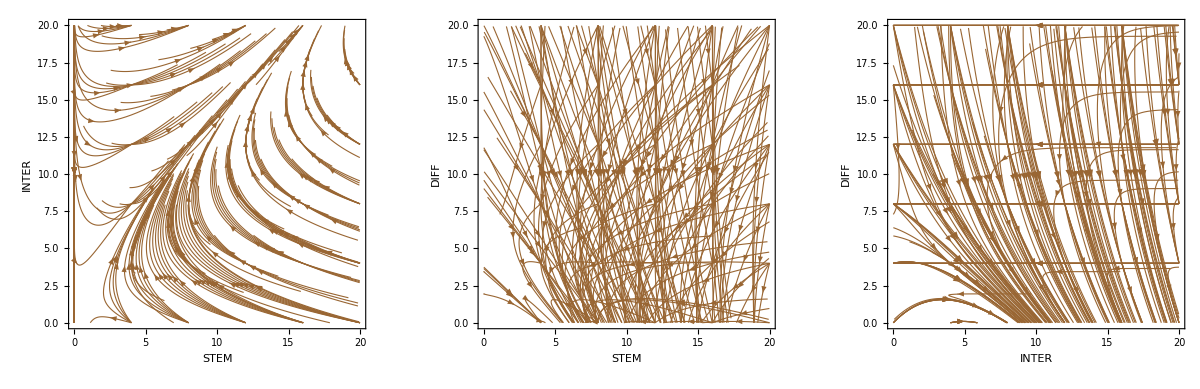

```mathematica
GraphicsRow[{DisplayFlow[DS1b, 100, StateVariables -> {STEM,INTER}],
DisplayFlow[DS1b, 100, StateVariables -> {STEM,DIFF}],
DisplayFlow[DS1b, 100, StateVariables -> {INTER,DIFF}]}]
```

```mathematica
DisplayPhasePortrait[DS1b]
```

-Graphics3D-

## Topology #1

Playing around with parameters:

```mathematica
(*Quiet[Manipulate[Show[DisplayPhasePortrait[DS1 /. {k1-> k1a,LS -> ls, PS -> ps,k2 -> k2a,LI -> li,k3 ->k3a,PI -> pi,Death-> d1}, SaddleManifolds -> True, Tries -> 10000], DisplayTrajectories[DS1/. {k -> k1,P -> p, L -> l, d -> d1},{{0,0},{0,5},{5,5},{5,0},{0,10},{10,10},{10,0},{0,15},{15,15},{15,0},{0,20},{20,20},{20,0},{10,20},{20,10}}, 100]], {k1a, 0,20,0.1},{ls, 0,1,0.1},{ps, 0,1,0.1},{k2a, 0,20,0.1},{li, 0,1,0.1},{k3a, 0,20,0.1},{pi, 0,1,0.1},{d1, 0,20,0.1}]])
```

Syntax::bktmop: Expression "Quiet[Manipulate[«1»,{k1a,0,20,0.1},{ls,0,1,0.1},{ps,0,1,0.1},{«1»},{li,0,1,0.1},{k3a,0,20,0.1},{pi,0,1,0.1},{d1,0,20,0.1}]])" has no opening "(".

## Phase Portrait

```mathematica
DS1a = DS1 /. {k1-> 5,LS ->0.5, PS -> 0.5,k2 ->5,LI ->0.5,k3 ->5,PI -> 0.5,Death-> 0.1};
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 0. and t = 0.000444065.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 30.0122 and t = 40.0122.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 40.0138 and t = 50.0138.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

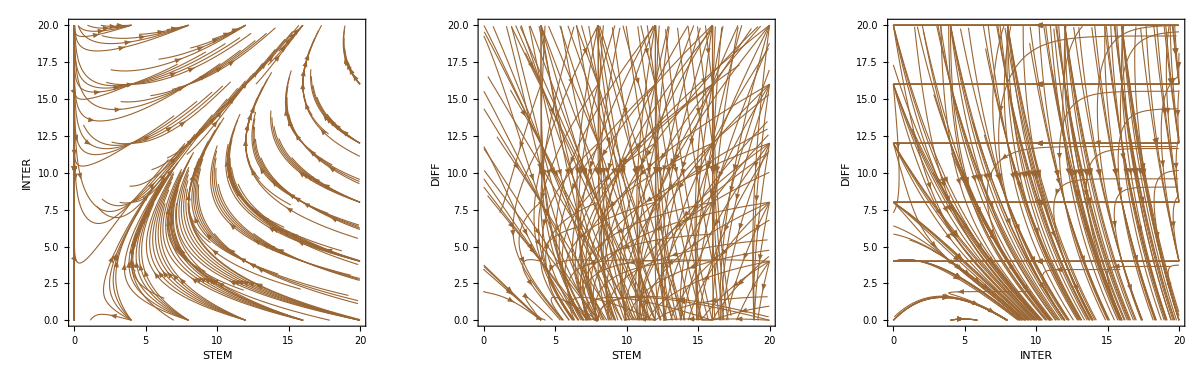

```mathematica
GraphicsRow[{DisplayFlow[DS1a, 100, StateVariables -> {STEM,INTER}],
DisplayFlow[DS1a, 100, StateVariables -> {STEM,DIFF}],
DisplayFlow[DS1a, 100, StateVariables -> {INTER,DIFF}]}]
(*Quiet[Show[DisplayFlow[DS1a, 100],DisplayPhasePortrait[DS1a, SaddleManifolds -> True]]])
```

```mathematica
DisplayPhasePortrait[DS1a, NullManifolds -> True]
```

-Graphics3D-

```mathematica
$BifurcationDiagramBPs
```

$BifurcationDiagramBPs

## Defining system using Lander control

1/(1+{a}*{pop})

```mathematica
Lander=DynamicalSystem[{LS*STEM*(1/(1 + a * STEM))-PS*2*LS*STEM*(1/(1+a*INTER)),PS*2*LS*STEM*(1/(1+a*INTER))+LI*STEM*(1/(1+a*DIFF))-PI*2*LI*STEM*1,PI*2*LI*STEM*1-Death*DIFF},{{STEM,0, 20},{DIFF,0,20}, {INTER, 0, 20}}, {{LS, 0, 10},{a, 0, 10}, {PS, 0, 10},{LI,0,10},{PI, 0,10},{Death,0,10} }];
```

```mathematica
Lander1 = Lander /. {LS -> 0.5, a -> 0.5, PS -> 0.5, LI -> 0.5, PI -> 0.5, Death -> 0.1};
```

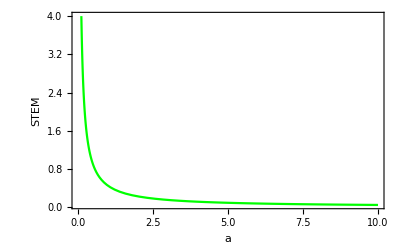

-Graphics-

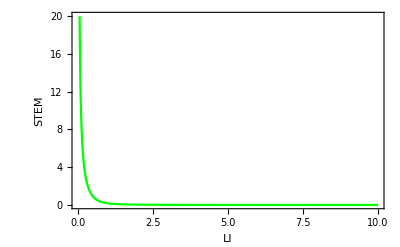

-Graphics-

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.99888,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,3.11672,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.66514,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.78009,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,2.38463,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.37729,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.0270512,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.425754,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.05077,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.2052,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,2.36615,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.631869,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.441095,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.892248,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.259944,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.577505,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.28364,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.25344,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,2.40592,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.70971,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,1.1562,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.591788,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.144464,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,2.26191,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,2.55014,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,0.207005,10}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,PI}={0,0,2.39314,10}

-Graphics-

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,2.36271,0.120393,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,3.32453,0.459041,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,7.44279,0.166045,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,9.17894,2.00152,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,9.45231,3.42496,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,9.52826,1.02827,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,10.2801,3.25077,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,10.9661,0.982056,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,11.2699,2.55517,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,11.7705,0.0153972,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,12.0258,2.71387,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,12.5487,3.85845,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,13.1859,3.15343,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,15.4422,1.45841,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {STEM,DIFF,INTER,Death}={0,19.8143,2.6497,0}

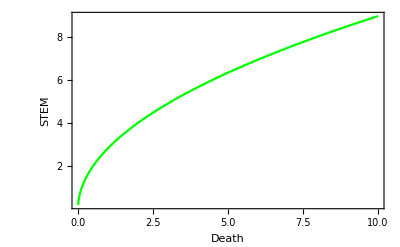

```mathematica
DisplayBifurcationDiagram[Lander1, a]
DisplayBifurcationDiagram[Lander1, LS]
DisplayBifurcationDiagram[Lander1, LI]
DisplayBifurcationDiagram[Lander1, PS]
DisplayBifurcationDiagram[Lander1, PI]
DisplayBifurcationDiagram[Lander1, Death]
```

```mathematica
Quiet[Manipulate[Show[DisplayPhasePortrait[Lander /. {a-> k1a,LS -> ls, PS -> ps,LI -> li,PI -> pi,Death-> d1}, SaddleManifolds -> True, Tries -> 10000], DisplayTrajectories[Lander/. {a-> k1a,LS -> ls, PS -> ps,LI -> li,PI -> pi,Death-> d1},{{0,0,5},{0,5,0},{5,5,5},{5,0,5},{0,10,10},{10,10,10},{10,0,0},{0,15,10},{15,15,10},{15,0,15},{0,20,10},{20,20,15},{20,0,20},{10,20,20},{20,10,20}}, 100]], {k1a, 0,20,0.1},{ls, 0,1,0.1},{ps, 0,1,0.1},{li, 0,1,0.1},{pi, 0,1,0.1},{d1, 0,20,0.1}]]
```

## Defining system using Hill control

```mathematica
Hill=DynamicalSystem[{L * STEM * (1/(1+a*STEM)^n) - P * 2 * L * STEM * (1/(1+a*DIFF)^n),P * 2 * L * STEM * (1/(1+a*DIFF)^n)- d * DIFF},{{STEM,0, 20},{DIFF,0,20}}, {{L, -10, 10},{a, -10, 10},{n, -10,10}, {P, -10, 10}, {d,-10,10} }];
```

```mathematica
Quiet[Manipulate[Show[DisplayPhasePortrait[Hill /. {a -> aa,n -> nn,P -> p, L -> l, d -> d1}, SaddleManifolds -> True], DisplayTrajectories[Hill/. {a -> aa,n -> nn, P -> p, L -> l, d -> d1},{{0,0},{0,5},{5,5},{5,0},{0,10},{10,10},{10,0},{0,15},{15,15},{15,0},{0,20},{20,20},{20,0},{10,20},{20,10}}, 100]], {aa, 0,20,0.1},{nn,-10,20},{p, 0,20,0.1},{l, 0,20,0.1},{d1, 0,20,0.1}]]
```

```mathematica
Hilla= Hill/.{L -> 1, a-> 2,n->2, P -> 1, d -> 0.1};
```

```mathematica
DisplayBifurcationDiagram[Hilla, a]
DisplayBifurcationDiagram[Hilla, n]
DisplayBifurcationDiagram[Hilla, L]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

## Define the System for topology #2

vES_2S = 3*STEM*(1-DIFF/8)
vES_D = 3*2*3*STEM*(STEM/8)
vED_D = 0.1*DIFF

dSTEM/dt = vES_2S - vES_D
dDIFF/dt = vES_D - vED_D

```mathematica
Topo2=DynamicalSystem[{L * STEM * (1-DIFF/k) - P * 2 * L * STEM * (STEM/k),P * 2 * L * STEM * (STEM/k)- d * DIFF},{{STEM,0, 20},{DIFF,0,20}}, {{L, -10, 10},{k, -10, 10}, {P, -10, 10}, {d,-10,10} }];
```

```mathematica
Quiet[Manipulate[Show[DisplayPhasePortrait[Topo2 /. {k -> k1,P -> p, L -> l, d -> d1}, SaddleManifolds -> True], DisplayTrajectories[Topo2/. {k -> k1,P -> p, L -> l, d -> d1},{{0,0},{0,5},{5,5},{5,0},{0,10},{10,10},{10,0},{0,15},{15,15},{15,0},{0,20},{20,20},{20,0},{10,20},{20,10}}, 100]], {k1, 0,20,0.1},{p, 0,20,0.1},{l, 0,20,0.1},{d1, 0,20,0.1}]]
```

## Bifurcation plots for system #2

```mathematica
second = Topo2/.{L -> 1, k-> 10, P -> 1, d -> 0.2};
```

```mathematica
DisplayBifurcationDiagram[second, k]
DisplayBifurcationDiagram[second, L]
DisplayBifurcationDiagram[second, d]
DisplayBifurcationDiagram[second, P]
```

Warning: A convergence failure occurred during continuation

-Graphics3D-

-Graphics3D-

Warning: A convergence failure occurred during continuation

-Graphics3D-

-Graphics3D-